```mathematica
{σ,ρ,β}={10.0,28.0,8/3.0};
TMax=100;
Timing[
{xSol,ySol,zSol}=NDSolveValue[{
x'[t]==σ (y[t]-x[t]),
y'[t]==x[t](ρ-z[t])-y[t],
z'[t]==x[t]y[t]-β z[t],
x[0]==1.0,
y[0]==0.0,
z[0]==0.0},
{x,y,z},
{t, 0, TMax}];
]
```

{0.046875,Null}

```mathematica
Lorenz[{x_,y_,z_}]:= {
σ (y-x),
x(ρ-z)-y,
x y-β z}
Timing[
xyzSol=NDSolveValue[{
xyz'[t]==Lorenz[xyz[t]],
xyz[0]=={1.0,0.0,0.0}
},
xyz,
{t, 0, TMax}];
]
```

{0.203125,Null}

```mathematica
Rober[{y1_,y2_,y3_}, {k1_,k2_,k3_}]:= {
-k1 y1 + k3 y2 y3,
k1 y1 -k2 y2^2 - k3 y2 y3,
k2  y2^2}
TMax=10.0^6;
Timing[
ySol=NDSolveValue[{
y'[t]==Rober[y[t],{0.04,3.0*10^7,1.0*10^4}],
y[0]=={1.0,0.0,0.0}
},
y,
{t, 0, TMax}];
]
```

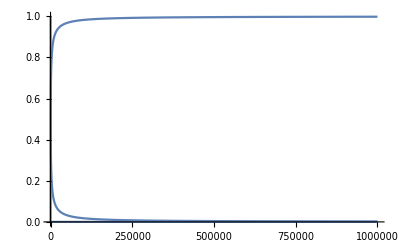

```mathematica
Plot[ ySol[t],{t, 0, TMax}]
```

```mathematica
J[{y1_,y2_,y3_}]=D[
Rober[{y1,y2,y3},{0.04,3.0*10^7,1.0*10^4}],
{{y1,y2,y3}}];
A=J[RandomReal[{0,1},3]];
MatrixForm[A]
Eigenvalues[A]
```

(-0.04 | 3980.67 | 7106.42
0.04 | -4.26425×10^7 | -7106.42
0 | 4.26385×10^7 | 0)

{-4.26354×10^7,-7106.98,9.56873×10^-13}